```mathematica
table = Import["/home/kacpert/Downloads/children_per_woman_total_fertility.csv"];
```

```mathematica
(*:>*)
```

```mathematica
years = table[[1 , 3;;]];
```

```mathematica
dataForPoland =Cases[table , {_ , "Poland" , rawData__}:>  {rawData}][[1]];
```

```mathematica
table//Dimensions
```

{196,303}

```mathematica
table//Length
```

196

```mathematica
years//Length
```

301

```mathematica
dataForPoland//Length
```

301

```mathematica
(*<= 1818 oraz >=2025*)
```

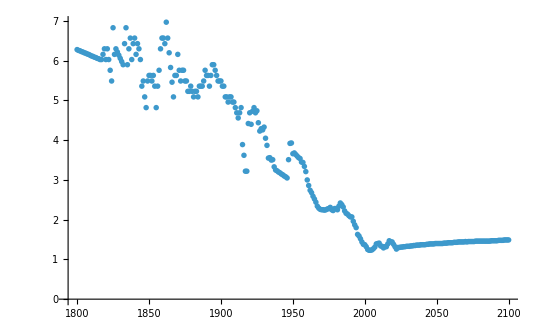

```mathematica
ListPlot[{years , dataForPoland}//Transpose]
```

```mathematica
Position[table[[1 , 3;;]] , 1817.]
```

{{18}}

```mathematica
Position[table[[1 , 3;;]] , 2025.]
```

{{226}}

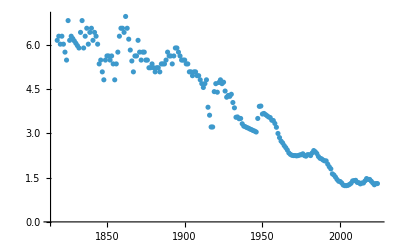

```mathematica
ListPlot[{years[[19;;225]] , dataForPoland[[19;;225]]}//Transpose]
```

```mathematica
Cases[table , {_ , _  , __  ,1817.,rawData__, 2025., __}:>{rawData}]
```

{{1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.,2001.,2002.,2003.,2004.,2005.,2006.,2007.,2008.,2009.,2010.,2011.,2012.,2013.,2014.,2015.,2016.,2017.,2018.,2019.,2020.,2021.,2022.,2023.,2024.}}

```mathematica
Position[table[[1 , 3;;]] , 1976.]
```

{{177}}

```mathematica
chpm = table[[2;; , 179]];
```

```mathematica
chpm//MinMax
```

{1.,8.42}

```mathematica
Count[table[[2;; , 179]] , x_/;x>7.]
```

28

```mathematica
Hold[FullForm[Count[table[[2;; , 179]] , x_/;x>7.]]]
```

Hold[Count[Part[table,Span[2,All],179],Condition[Pattern[x,Blank[]],Greater[x,7.]]]]

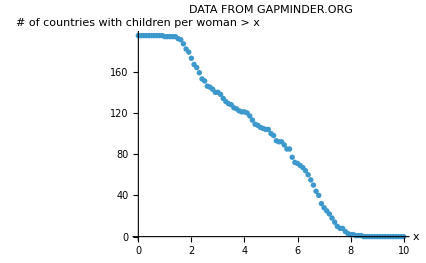

```mathematica
ListPlot[
Table[
{
chpw,
Count[table[[2;; , 179]] , x_/;x>chpw]
} , {chpw , 0 , 10 , 0.1}],
AxesLabel->{"x" ,"# of countries with children per woman > x"},
PlotLabel->"DATA FROM GAPMINDER.ORG"
]
```

```mathematica
a = Cases[table[[2;;]] , {_ , c_ , xs__}/;{xs}[[177]]>5 :>c]
```

{Afghanistan,Angola,UAE,Burundi,Benin,Burkina Faso,Bangladesh,Bahrain,Belize,Bolivia,Bhutan,Botswana,Central African Republic,Cote d'Ivoire,Cameroon,Congo, Dem. Rep.,Congo, Rep.,Comoros,Cape Verde,Djibouti,Dominican Republic,Algeria,Ecuador,Egypt,Eritrea,Ethiopia,Micronesia, Fed. Sts.,Gabon,Ghana,Guinea,Gambia,Guinea-Bissau,Equatorial Guinea,Guatemala,Honduras,Haiti,India,Iran,Iraq,Jordan,Kenya,Kuwait,Lao,Liberia,Libya,St. Lucia,Lesotho,Morocco,Madagascar,Maldives,Mexico,Marshall Islands,Mali,Myanmar,Mongolia,Mozambique,Mauritania,Malawi,Namibia,Niger,Nigeria,Nicaragua,Nepal,Oman,Pakistan,Peru,Philippines,Papua New Guinea,Paraguay,Palestine,Qatar,Rwanda,Saudi Arabia,Sudan,Senegal,Solomon Islands,Sierra Leone,El Salvador,Somalia,South Sudan,Sao Tome and Principe,Eswatini,Syria,Chad,Togo,Tajikistan,Turkmenistan,Timor-Leste,Tonga,Tunisia,Tanzania,Uganda,Uzbekistan,Vietnam,Vanuatu,Samoa,Yemen,South Africa,Zambia,Zimbabwe}

```mathematica
listOfCountries = {};
```

```mathematica
hasCHPWgt5[{_ , c_ , xs__}/;{xs}[[177]]>5]:=AppendTo[listOfCountries , c];
```

```mathematica
hasCHPWgt5/@table[[2;;]];
```

```mathematica
listOfCountries//Sort
```

{Afghanistan,Algeria,Angola,Bahrain,Bangladesh,Belize,Benin,Bhutan,Bolivia,Botswana,Burkina Faso,Burundi,Cameroon,Cape Verde,Central African Republic,Chad,Comoros,Congo, Dem. Rep.,Congo, Rep.,Cote d'Ivoire,Djibouti,Dominican Republic,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Eswatini,Ethiopia,Gabon,Gambia,Ghana,Guatemala,Guinea,Guinea-Bissau,Haiti,Honduras,India,Iran,Iraq,Jordan,Kenya,Kuwait,Lao,Lesotho,Liberia,Libya,Madagascar,Malawi,Maldives,Mali,Marshall Islands,Mauritania,Mexico,Micronesia, Fed. Sts.,Mongolia,Morocco,Mozambique,Myanmar,Namibia,Nepal,Nicaragua,Niger,Nigeria,Oman,Pakistan,Palestine,Papua New Guinea,Paraguay,Peru,Philippines,Qatar,Rwanda,Samoa,Sao Tome and Principe,Saudi Arabia,Senegal,Sierra Leone,Solomon Islands,Somalia,South Africa,South Sudan,St. Lucia,Sudan,Syria,Tajikistan,Tanzania,Timor-Leste,Togo,Tonga,Tunisia,Turkmenistan,UAE,Uganda,Uzbekistan,Vanuatu,Vietnam,Yemen,Zambia,Zimbabwe}

```mathematica
a//Sort
```

{Afghanistan,Algeria,Angola,Bahrain,Bangladesh,Belize,Benin,Bhutan,Bolivia,Botswana,Burkina Faso,Burundi,Cameroon,Cape Verde,Central African Republic,Chad,Comoros,Congo, Dem. Rep.,Congo, Rep.,Cote d'Ivoire,Djibouti,Dominican Republic,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Eswatini,Ethiopia,Gabon,Gambia,Ghana,Guatemala,Guinea,Guinea-Bissau,Haiti,Honduras,India,Iran,Iraq,Jordan,Kenya,Kuwait,Lao,Lesotho,Liberia,Libya,Madagascar,Malawi,Maldives,Mali,Marshall Islands,Mauritania,Mexico,Micronesia, Fed. Sts.,Mongolia,Morocco,Mozambique,Myanmar,Namibia,Nepal,Nicaragua,Niger,Nigeria,Oman,Pakistan,Palestine,Papua New Guinea,Paraguay,Peru,Philippines,Qatar,Rwanda,Samoa,Sao Tome and Principe,Saudi Arabia,Senegal,Sierra Leone,Solomon Islands,Somalia,South Africa,South Sudan,St. Lucia,Sudan,Syria,Tajikistan,Tanzania,Timor-Leste,Togo,Tonga,Tunisia,Turkmenistan,UAE,Uganda,Uzbekistan,Vanuatu,Vietnam,Yemen,Zambia,Zimbabwe}

```mathematica
% == %%
```

True

```mathematica
hasCHPWgt5[table[[13]]]
```

Burundi

```mathematica
Position[table , {_ , "Burundi" , __}]
```

{{13}}

```mathematica
f/@{1 , 2 , 3 , 4 ,5}
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
list = {};
```

```mathematica
AppendTo[list , 321]
```

{123,321}

```mathematica
list
```

{123,321}

```mathematica
Riffle[{1 , 3 , 5 , 7} , {2 , 4 , 6 , 8}]
```

{1,2,3,4,5,6,7,8}

```mathematica
Partition[Riffle[{1 , 3 , 5 , 7} , {2 , 4 , 6 , 8}] , 2]
```

{{1,2},{3,4},{5,6},{7,8}}

```mathematica
{{1 , 3 , 5 , 7} , {2 , 4 , 6 , 8}}//Transpose
```

{{1,2},{3,4},{5,6},{7,8}}

```mathematica
Table[g[i , j] , {i , 1 , 3} , {j , 1 , 2}]
```

{{g[1,1],g[1,2]},{g[2,1],g[2,2]},{g[3,1],g[3,2]}}

```mathematica
Array[g , {3 , 2}]
```

{{g[1,1],g[1,2]},{g[2,1],g[2,2]},{g[3,1],g[3,2]}}

```mathematica
f[x_]:= Sin[x^2 + Cos[2.] π/x];
```

```mathematica
f[2.]
```

-0.203298

```mathematica
fM[x_]:=Module[{a , b},
a = x^2;
b = Cos[2.] π/x;
Sin[a + b]
];
```

```mathematica
fM[2.]
```

-0.203298

```mathematica
a
```

{Afghanistan,Angola,UAE,Burundi,Benin,Burkina Faso,Bangladesh,Bahrain,Belize,Bolivia,Bhutan,Botswana,Central African Republic,Cote d'Ivoire,Cameroon,Congo, Dem. Rep.,Congo, Rep.,Comoros,Cape Verde,Djibouti,Dominican Republic,Algeria,Ecuador,Egypt,Eritrea,Ethiopia,Micronesia, Fed. Sts.,Gabon,Ghana,Guinea,Gambia,Guinea-Bissau,Equatorial Guinea,Guatemala,Honduras,Haiti,India,Iran,Iraq,Jordan,Kenya,Kuwait,Lao,Liberia,Libya,St. Lucia,Lesotho,Morocco,Madagascar,Maldives,Mexico,Marshall Islands,Mali,Myanmar,Mongolia,Mozambique,Mauritania,Malawi,Namibia,Niger,Nigeria,Nicaragua,Nepal,Oman,Pakistan,Peru,Philippines,Papua New Guinea,Paraguay,Palestine,Qatar,Rwanda,Saudi Arabia,Sudan,Senegal,Solomon Islands,Sierra Leone,El Salvador,Somalia,South Sudan,Sao Tome and Principe,Eswatini,Syria,Chad,Togo,Tajikistan,Turkmenistan,Timor-Leste,Tonga,Tunisia,Tanzania,Uganda,Uzbekistan,Vietnam,Vanuatu,Samoa,Yemen,South Africa,Zambia,Zimbabwe}

```mathematica
Hold[FullForm[Module[{a , b},
a = x^2;
b = Cos[2.] π/x;
Sin[a + b]
]]]
```

Hold[Module[List[a,b],CompoundExpression[Set[a,Power[x,2]],Set[b,Times[Cos[2.],Times[Pi,Power[x,-1]]]],Sin[Plus[a,b]]]]]

```mathematica
Hold[FullForm[a = x^2;
b = Cos[2.] π/x;
Sin[a + b]]]
```

Hold[CompoundExpression[Set[a,Power[x,2]],Set[b,Times[Cos[2.],Times[Pi,Power[x,-1]]]],Sin[Plus[a,b]]]]

```mathematica
x = 2.;
a = x^2;
b = Cos[2.] π/x;
Sin[a + b]
```

-0.203298

```mathematica
a
```

4.

```mathematica
?For
```

```mathematica
For[
i = 0 , i< 22 , i = i + 1 , 
Print[i]
]
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

```mathematica
Do[Print[i] , {i , 0 , 21}]
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21